## Week 7 - Lecture 5: The Monte Carlo Method - Basics

Resources  --  Video  &&  Notes 7e

2D Linear Systems: Recap of General Theory (Page 2-3)

#### Random Systems: A first look at MC approach

Check page 4. Let us now generate many random 2x2 matrices and try to estimate the probability of each type of fixed point.
RandomReal[] gives a random real number between 0 to 1. To get a uniform distribution in [-1, 1] -> 2RR[]-1

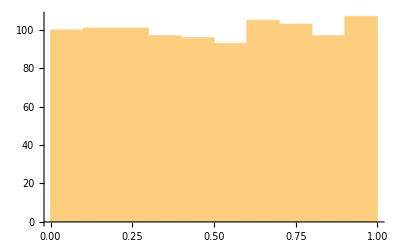

```mathematica
Histogram[Table[RandomReal[], {1000}]]
```

We see that it roughly corresponds to an uniform distribution.

```mathematica
UnitStep[1]
```

1

```mathematica
UnitStep[0.1]
```

1

```mathematica
UnitStep[0]
```

1

```mathematica
UnitStep[-0.1]
```

0

Computing the probabilities

```mathematica
data = Table[
alist = Table[2(RandomReal[]-0.5), {i,1,Nmat}];
blist = Table[2(RandomReal[]-0.5), {i,1,Nmat}];
clist = Table[2(RandomReal[]-0.5), {i,1,Nmat}];
dlist = Table[2(RandomReal[]-0.5), {i,1,Nmat}];
deltalist = alist*dlist-blist*clist; (* Δ = Det(A) *)
taulist = alist+dlist; (* τ=Trace(A) *)
disclist = taulist*taulist-4*deltalist; (* Discriminant: τ^2-4Δ *)
fracsaddle = Total[1-UnitStep[deltalist]]/Nmat // N; (* Fraction of cases with Δ<0 *)
(* Fraction of Unstable Nodes: Δ>0 & τ>0 & Discriminant>0 *)
fracunstablenode = Total[UnitStep[deltalist]UnitStep[taulist]UnitStep[disclist]]/Nmat // N;
{Nmat, fracsaddle, fracunstablenode}, {Nmat, 100000,1000000,100000}]
```

{{100000,0.50108,0.09035},{200000,0.50164,0.090685},{300000,0.498727,0.0909667},{400000,0.49948,0.090025},{500000,0.500394,0.09054},{600000,0.500072,0.08949},{700000,0.501236,0.0899714},{800000,0.50094,0.0898875},{900000,0.500093,0.08985},{1000000,0.500454,0.089954}}

```mathematica
ListLinePlot[data[[All, {1,3}]]] 
(*For all data points, point column 1 vs column 3 [nMat vs UnstableNode%] *)
Mean[data[[;;,3]]]  (*Average estimate of Probability *)
```

-Graphics-

0.090172

```mathematica
ListLinePlot[data[[All, {1,2}]]] 
Mean[data[[;;,2]]]  (*Average estimate of Probability. Should -> 0.5 *)
```

-Graphics-

0.500412

Homework:
- Try for all cases of Δ, τ, Discriminant and check their probabilities.
- Try playing with Nmat, compute error bars (say std), etc. and make a table